```mathematica
ClearAll["Global'*"]

WIN=0;

If[WIN==1,
scenario="outputs\\scenario2\\";
fileIDM="IDM - x0=0.0 - v0=11.0.txt";,
scenario="outputs/scenario2/";
fileIDM="IDM - x0=0.0 - v0=11.0.txt";
]

dataFolder=StringJoin[NotebookDirectory[],scenario];
SetDirectory[dataFolder];files=FileNames[ ];Length[files];
(* Import IDM data *)
dataIDM=Import[fileIDM,"Table"];
(* Import SDP data *)
pos={};speed={};accel={};vmin={};vmax={};xmin={};xmax={};initx={};initv={};inita={};
For[i=1,i≤Length[files]-1,i++,
If[files[[i]]=="idm" ||files[[i]]==".DS_Store" ,Continue[]];
data=Import[files[[i]],"Table"];
steps=data[[2;;,1]];
controlSteps=Delete[data[[2;;,1]],Length[steps]];
AppendTo[pos,data[[2;;,2]]];
AppendTo[speed,data[[2;;,3]]];
AppendTo[accel,Drop[data[[2;;,4]],-1]];
AppendTo[vmin,data[[2;;,13]]];
AppendTo[vmax,data[[2;;,14]]];
AppendTo[xmin,data[[2;;,15]]];
AppendTo[xmax,data[[2;;,16]]];
AppendTo[initv,data[[2;;,17]]];
AppendTo[initx,data[[2;;,18]]];
AppendTo[inita,Drop[data[[2;;,19]],-1]];
]
```

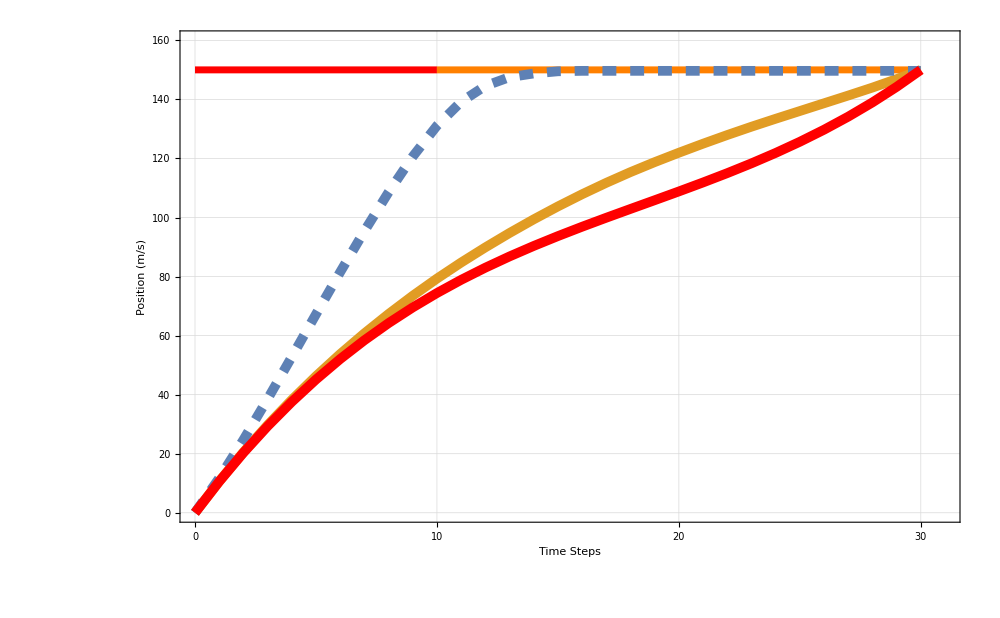

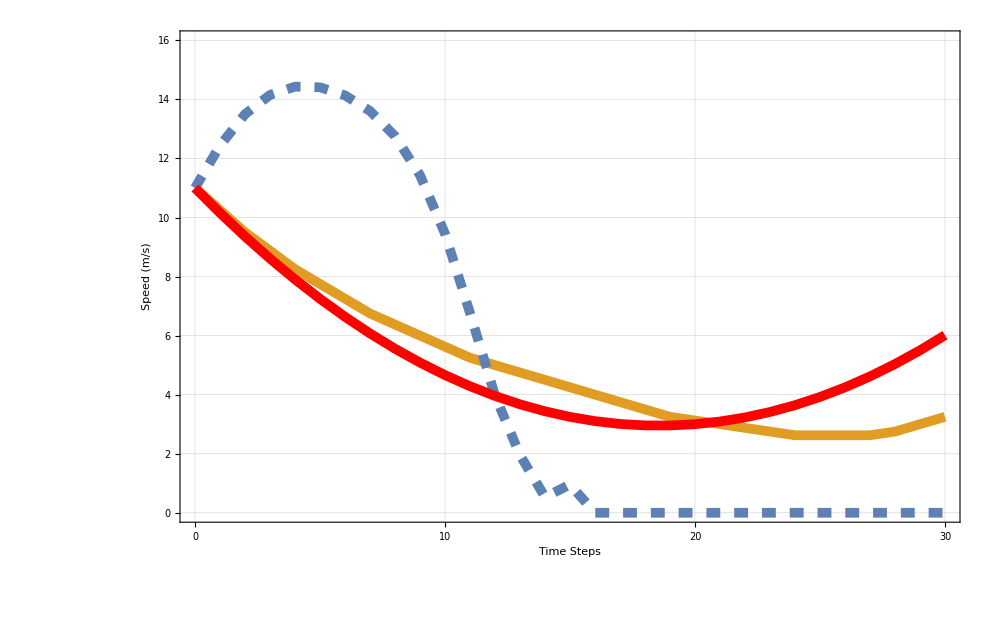

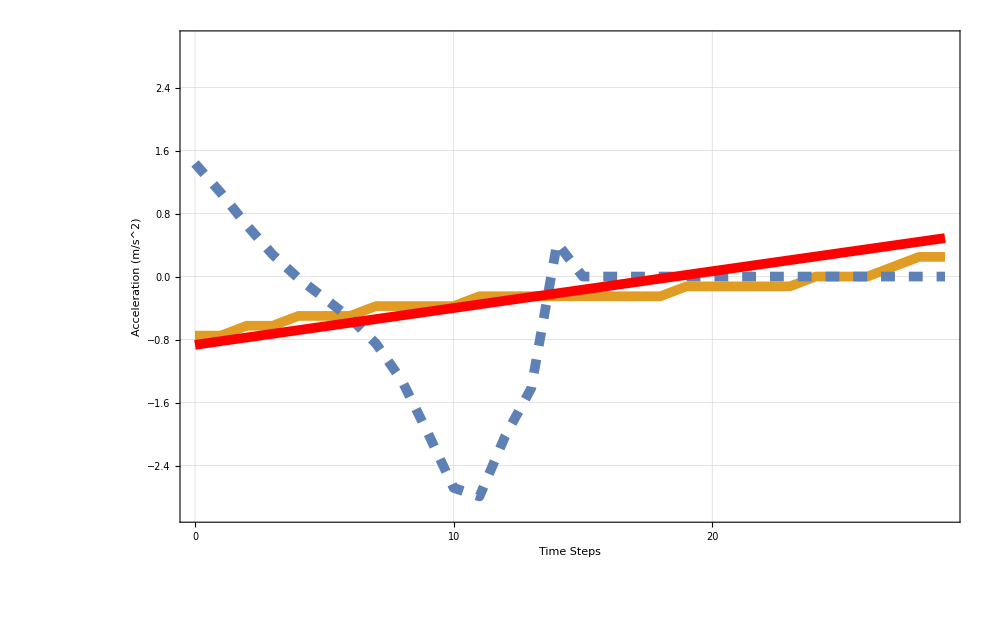

```mathematica
(*controlSteps;
plotsV={};
For[i=1,i≤Length[files],i++,
AppendTo[plotsV,
Show[
ListLinePlot[{Transpose[{steps,speed[[i]]}]},PlotRange->{Automatic,{0,11}},
LabelStyle->{FontFamily->"Constantia", FontSize->28,Bold},PlotStyle->{{Thickness[0.005],ColorData[97,"ColorList"][[2]]}},
TicksStyle->Directive[FontSize->24],AxesStyle->Thickness[0.001],
Frame->{True,True,False,False},FrameLabel->{"Time Steps","Speed (m/s)",None,None}],
ListLinePlot[{Transpose[{steps,initv[[i]]}]},PlotStyle->{{Dashed,Thickness[0.005]}}],
ListLinePlot[{Transpose[{steps,vmin[[i]]}]},PlotStyle->{{Thickness[0.005],Red,Dashed}}],
ListLinePlot[{Transpose[{steps,vmax[[i]]}]},PlotStyle->{{Thickness[0.005],Dashed,Red}}],
ImageSize->1000]]]
plotsV;*)

defBlue=ColorData[97,1];
defOrange=ColorData[97,2];
defGreen=ColorData[97,3];
fontSize=58;

n = Length[files];
SetDirectory[NotebookDirectory[]];
(*For[i=1,i≤n,i++,
llp=ListLinePlot[{Transpose[{controlSteps,accel[[i]]}],Transpose[{controlSteps,inita[[i]]}]},
Filling->None,
Joined->True,
GridLines->{{0,10,20,30},{-0.5,-0.25,0,0.25,0.5}},
PlotRange->{{0,30},{-0.55,0.55}},
LabelStyle->{FontFamily->"Constantia", FontSize->fontSize-6,Bold},
PlotStyle->{{Thickness[0.007],defOrange},{Thickness[0.007],Dashing[0.01],defBlue}},
AxesStyle->Thickness[0.001],
ImageSize->1000,
PlotStyle->PointSize[Large],
Frame->{True,True,False,False},
FrameTicks->{{{-0.5,-0.25,0,0.25,0.5},None},{{0,10,20,30},None}},
FrameLabel->{"Time Steps","Acceleration (m/s^2)",None,None}
];
llp2=ListLinePlot[{Transpose[{steps,speed[[i]]}],Transpose[{steps,initv[[i]]}],Transpose[{steps,vmax[[i]]}],Transpose[{steps,vmin[[i]]}]},
Filling->None,
Joined->True,
GridLines->Automatic,
PlotRange->{Automatic,{0,10.5}},
LabelStyle->{FontFamily->"Constantia", FontSize->fontSize,Bold},
PlotStyle->{{Thickness[0.007],defOrange},{Thickness[0.007],Dashing[0.01],defBlue},{Thickness[0.007],Dashing[0.01],Red},{Thickness[0.007],Dashing[0.01],Red}},
AxesStyle->Thickness[0.001],
ImageSize->1000,
PlotStyle->PointSize[Large],
Frame->{True,True,False,False},
FrameTicks->{{Automatic,None},{{0,10,20,30},None}},
FrameLabel->{"Time Steps","Speed (m/s)",None,None}
];
(*Export["speed-"<>ToString[i]<>".png",llp2,ImageResolution->100];
Export["accel-"<>ToString[i]<>".png",llp,ImageResolution->100]*)
]

For[i=1,i≤n,i++,
llp=ListLinePlot[{Transpose[{controlSteps,accel[[i]]}],Transpose[{controlSteps,accel[[6]]}]},
Filling->None,
Joined->True,
GridLines->{{0,10,20,30},{-0.5,-0.25,0,0.25,0.5}},
PlotRange->{{0,30},{-0.55,0.55}},
LabelStyle->{FontFamily->"Constantia", FontSize->fontSize-6,Bold},
PlotStyle->{{Thickness[0.007],defOrange},{Thickness[0.007],Dashing[0.01],defBlue}},
AxesStyle->Thickness[0.001],
ImageSize->1000,
PlotStyle->PointSize[Large],
Frame->{True,True,False,False},
FrameTicks->{{{-0.5,-0.25,0,0.25,0.5},None},{{0,10,20,30},None}},
FrameLabel->{"Time Steps","Acceleration (m/s^2)",None,None}
];
llp2=ListLinePlot[{Transpose[{steps,speed[[i]]}],Transpose[{steps,speed[[6]]}]},
Filling->None,
Joined->True,
GridLines->Automatic,
PlotRange->{Automatic,{0,10.5}},
LabelStyle->{FontFamily->"Constantia", FontSize->fontSize,Bold},
PlotStyle->{{Thickness[0.007],defOrange},{Thickness[0.007],Dashing[0.01],defBlue}},
AxesStyle->Thickness[0.001],
ImageSize->1000,
PlotStyle->PointSize[Large],
Frame->{True,True,False,False},
FrameTicks->{{Automatic,None},{{0,10,20,30},None}},
FrameLabel->{"Time Steps","Speed (m/s)",None,None}
];
(*Export["DDDPvsSDP-speed-"<>ToString[i]<>".png",llp2,ImageResolution->100];
Export["DDDPvsSDP-accel-"<>ToString[i]<>".png",llp,ImageResolution->100]*)
];*)


(* Last Iteration Plots VS IDM *)

(* Position *)
redTrafPos=Table[150,{i,0,10}];steps1=Table[i,{i,0,10}];
orangeTrafPos=Table[150,{i,10,steps[[-1]]}];steps2=Table[i,{i,10,steps[[-1]]}];
Show[
ListLinePlot[{Transpose[{steps1,redTrafPos}]},Filling->None,Joined->True,GridLines->Automatic,PlotRange->{{steps[[1]],steps[[-1]]+1},{0,160}},LabelStyle->{FontFamily->"Constantia", FontSize->fontSize,Bold},PlotStyle->{{Thickness[0.005],Red}},AxesStyle->Thickness[0.001],ImageSize->1000,PlotStyle->PointSize[Large],Frame->{True,True,False,False},FrameTicks->{{Automatic,None},{{0,10,20,30},None}},FrameLabel->{"Time Steps","Position (m/s)",None,None}],
ListLinePlot[{Transpose[{steps2,orangeTrafPos}]},PlotStyle->{{Thickness[0.005],Orange}}],
ListLinePlot[{Transpose[{steps,pos[[n-3]]}],Transpose[{steps,dataIDM[[1;;,2]]}],Transpose[{steps,initx[[1]]}]},
PlotRange->{Automatic,{0,160}},
LabelStyle->{FontFamily->"Constantia", FontSize->fontSize,Bold},
PlotStyle->{{Thickness[0.007],defOrange},{Thickness[0.007],Dashing[0.01],defBlue},{Thickness[0.007],Red}},Filling->None,Joined->True,GridLines->Automatic,
AxesStyle->Thickness[0.001],ImageSize->1000,PlotStyle->PointSize[Large],Frame->{True,True,False,False},FrameTicks->{{Automatic,None},{{0,10,20,30},None}},FrameLabel->{"Time Steps","Position (m)",None,None}]
]
(* Speed *)
ListLinePlot[{Transpose[{steps,speed[[n-3]]}],Transpose[{steps,dataIDM[[1;;,3]]}],Transpose[{steps,initv[[1]]}]},Filling->None,Joined->True,GridLines->Automatic,
PlotRange->{Automatic,{0,16}},
LabelStyle->{FontFamily->"Constantia", FontSize->fontSize,Bold},
PlotStyle->{{Thickness[0.007],defOrange},{Thickness[0.007],Dashing[0.01],defBlue},{Thickness[0.007],Red}},
AxesStyle->Thickness[0.001],ImageSize->1000,PlotStyle->PointSize[Large],Frame->{True,True,False,False},FrameTicks->{{Automatic,None},{{0,10,20,30},None}},FrameLabel->{"Time Steps","Speed (m/s)",None,None}]
(* Acceleration *)
ListLinePlot[{Transpose[{controlSteps,accel[[n-3]]}],Transpose[{controlSteps,dataIDM[[1;;-2,4]]}],Transpose[{controlSteps,inita[[1]]}]},Filling->None,Joined->True,GridLines->Automatic,
PlotRange->{Automatic,{-3,3}},
LabelStyle->{FontFamily->"Constantia", FontSize->fontSize,Bold},
PlotStyle->{{Thickness[0.007],defOrange},{Thickness[0.007],Dashing[0.01],defBlue},{Thickness[0.007],Red}},
AxesStyle->Thickness[0.001],ImageSize->1000,PlotStyle->PointSize[Large],Frame->{True,True,False,False},FrameTicks->{{Automatic,None},{{0,10,20,30},None}},FrameLabel->{"Time Steps","Acceleration (m/s^2)",None,None}]
```